```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[];DateObject[];
```

```mathematica
(*ToExpression[Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\2-Normal state\\dispersion_6Al_soc=0.00.txt",{"TSV","Data",All,1;;2},"NumberPoint"->","]];*)
```

{μ→-0.410202,b→0,c→3.50867}

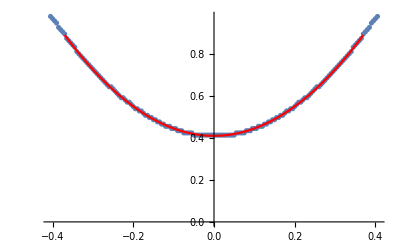

7.51066-7.10115 Cos[k]

```mathematica
"-------------Normal state Aluminum---------------";
Alumin=Flatten[Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\2-Normal state\\dispersion_6Al_soc=0.00.mat"],1];
(*DataFinal=Flatten[data1,1];
DataFinal*)
Alumin;
AL1=ListPlot[Alumin];
modelAl=(*g *k^6+f *k^5+e *k^4+d *k^3+*)c *k^2+b*k-μ;
FitAl=Chop[FindFit[Alumin,modelAl,{μ,b,c(*,d,e,f,g*)},k]]

(*MatrixForm[NumberForm[FitAl,3]]*)

FAL=Function[{t},Evaluate[modelAl/.FitAl]];
AL2=Plot[FAL[k],{k,-0.37,0.37},PlotStyle->{Red},PlotRange->{{-0.37,0.37},{0,1}}];
Show[AL1,AL2]

FindFormula[Alumin,k]
```

```mathematica
NumberForm[0.41020196058761277+3.508670885456279 k^2.,3]
```

0.41+3.51 k^2.

{μ→0.6349,b→0,c→12.03}

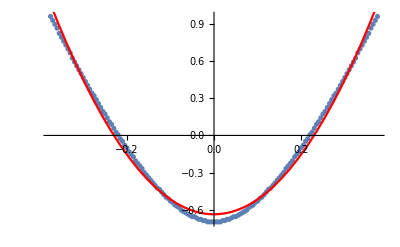

-0.692661+16.8918 k^2-59.432 k^4+165.609 k^6

```mathematica
"-------------Normal state Au(111) surface states---------------";
Gold=Flatten[Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\2-Normal state\\dispersion_Au111_soc=0.00.mat"],1];
(*DataFinal=Flatten[data1,1];
DataFinal*)
Gold;
Au1=ListPlot[Gold];
modelAu111=(*g *k^6+f *k^5+e *k^4+e *k^4+d *k^3+*)c *k^2+b*k-μ;
FitAu111=Chop[FindFit[Gold,modelAu111,{μ,b,c(*,d,e,f,g*)},k]];

MatrixForm[NumberForm[FitAu111,4]]

FAU=Function[{t},Evaluate[modelAu111/.FitAu111]];
Au111=Plot[FAU[k],{k,-0.5,0.5},PlotStyle->{Red},PlotRange->{{-0.5,0.5},{-2,2}}];
Show[Au1,Au111]

FindFormula[Gold,k]
```

----For only Spin Up section------------

{c→20.2,b→0.748,μ→0.831}

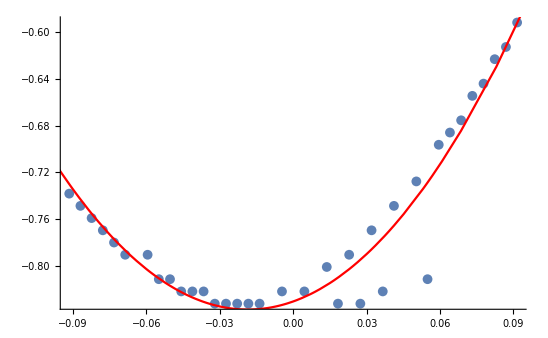

-0.766434

```mathematica
"-------------Rashba bands in hybrid structure---------------";
"----For only Spin Up section------------"
Rashba=Flatten[Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\0-Manipulated data by me\\Rashba_SpinUP.mat"],1];
PltR=ListPlot[Rashba];
modelR=(*g *k^6+f *k^5+e *k^4+d *k^3+*)c *k^2+b*k-μ;
FitR=Chop[FindFit[Rashba,modelR,{(*g,f,e,d,*)c,b,μ},k]];


NumberForm[FitR,3]

PP=Function[{t},Evaluate[modelR/.FitR]];
PLLot=Plot[PP[k],{k,-0.37,0.37},PlotStyle->{Red}];
Show[PltR,PLLot]

FindFormula[Rashba,kx]
```

----For only Spin down section------------

{c→20.1,b→-0.738,μ→0.832}

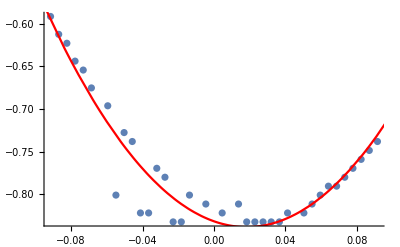

-0.76847

```mathematica
"-------------Rashba bands in hybrid structure---------------";
"----For only Spin down section------------"
RashbaDown=Flatten[Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\0-Manipulated data by me\\Rashba_SpinDown.mat"],1];
PltD=ListPlot[RashbaDown];
modelD=(*g *k^6+f *k^5+e *k^4+d *k^3+*)c *k^2+b*k-μ;
FitD=Chop[FindFit[RashbaDown,modelD,{(*g,f,e,d,*)c,b,μ},k]];


NumberForm[FitD,3]

DD=Function[{t},Evaluate[modelD/.FitD]];
PLLotD=Plot[DD[k],{k,-0.37,0.37},PlotStyle->{Red}];
Show[PltD,PLLotD]

FindFormula[RashbaDown,kx]
```

----For only Spin down section------------

{c→6.79,b→0.136,μ→0.112}

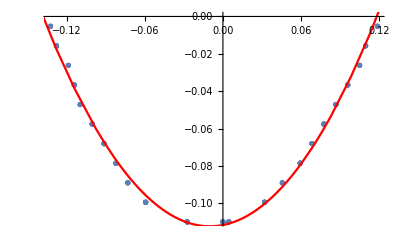

-0.11118+0.197308 kx+6.64739 kx^2-6.08514 kx^3

```mathematica
"-------------Spin Spilit Al bands---------------";
"----For only Spin down section------------"
AluminumDown=Flatten[Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\0-Manipulated data by me\\Aluminum_SpinDown.mat"],1];
ALD=ListPlot[AluminumDown];
modelAlD=(*g *k^6+f *k^5+e *k^4+d *k^3+*)c *k^2+b*k-μ;
FitAlD=Chop[FindFit[AluminumDown,modelAlD,{(*g,f,e,d,*)c,b,μ},k]];


NumberForm[FitAlD,3]

AlD=Function[{t},Evaluate[modelAlD/.FitAlD]];
PLLotAlD=Plot[AlD[k],{k,-0.37,0.37},PlotStyle->{Red}];
Show[ALD,PLLotAlD]

FindFormula[AluminumDown,kx]
```

----For only Spin down section------------

{c→6.79,b→-0.136,μ→0.112}

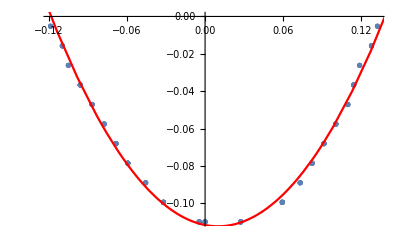

-0.11118-0.197308 kx+6.64739 kx^2+6.08514 kx^3

```mathematica
"-------------Spin Spilit Al bands---------------";
"----For only Spin down section------------"
AluminumUp=Flatten[Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\0-Manipulated data by me\\Aluminum_SpinUP.mat"],1];
ALU=ListPlot[AluminumUp];
modelAlU=(*g *k^6+f *k^5+e *k^4+d *k^3+*)c *k^2+b*k-μ;
FitAlU=Chop[FindFit[AluminumUp,modelAlU,{(*g,f,e,d,*)c,b,μ},k]];


NumberForm[FitAlU,3]

AlU=Function[{t},Evaluate[modelAlU/.FitAlU]];
PLLotAlU=Plot[AlU[k],{k,-0.37,0.37},PlotStyle->{Red}];

Show[ALU,PLLotAlU]

FindFormula[AluminumUp,kx]
```

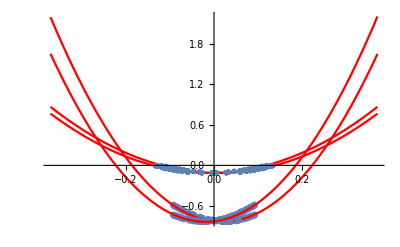

```mathematica
Show[PLLotAlU,PLLotAlD,ALU,ALD,PltD,PLLotD,PltR,PLLot,PlotStyle->{Blue,Red},PlotRange->{{-0.1,0.1},{Automatic,0}}]
(*Show[ALU,ALD,PlotRange->{{-0.1,0.1},{Automatic,0}}]*)
```

----For only Spin Up section------------

{c→17.3,b→0.782,μ→0.733}

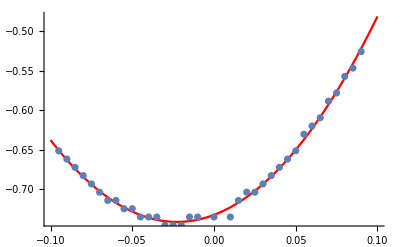

-0.732793+0.782469 kx+17.2987 kx^2

```mathematica
"-------------Rashba bands isolated---------------";
"----For only Spin Up section------------"
RashIso=Flatten[Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\0-Manipulated data by me\\Rashba_No_Hybridization.mat"],1];
Q1=ListPlot[RashIso];
modelIso=(*g *k^6+f *k^5+e *k^4+d *k^3+*)c *k^2+b*k-μ;
FitY=Chop[FindFit[RashIso,modelIso,{(*g,f,e,d,*)c,b,μ},k]];


NumberForm[FitY,3]

II=Function[{t},Evaluate[modelIso/.FitY]];
Pl=Plot[II[k],{k,-0.1,0.1},PlotStyle->{Red}];
Show[Pl,Q1]

FindFormula[RashIso,kx]
```

```mathematica
"------Crossing points---------";
Solve["0.41"+"3.51" k^("2.")==-0.635+12 k^2,k]
```

{{k→-0.350843},{k→0.350843}}

```mathematica
Head@Alumin[[3,1]]
```

Part

```mathematica
data1[[1,1]]
```

-0.020000000000000018

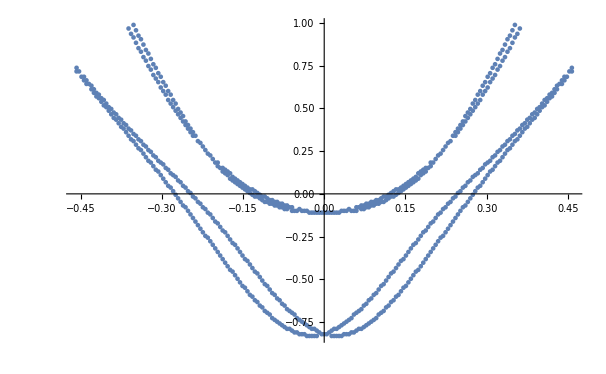

```mathematica
"-----Normal-state------with Spin-orbit coupling-----";
AuAl=Flatten[Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\dispersion_6Au_6Al.mat"],1];
Show[ListPlot[AuAl](*,AL2,Au111*)]
```

```mathematica
"---------------------Normal state DFT and model--------------------";
Manipulate[

Fig1=ListLinePlot[Transpose[(*Table[*)Table[Flatten[{Join[(*({{k}, {k}, {k}, {k}})*)({{kx}, {kx}, {kx}, {kx}})],Sort[Eigenvalues[({{(kx^2+ky^2) Aluminium-MAl, 0, f0, 0}, {0, (kx^2+ky^2) Aluminium-MAl, 0, f0}, {f0, 0, (kx^2+ky^2) Gold-Mgold, (ⅈ kx+ky) λ}, {0, f0, (-ⅈ kx+ky) λ, (kx^2+ky^2) Gold-Mgold}})],Greater]
},{{2},{1}}],{kx,-0.1,0.1,1/300}](*,{Δ,0,3}]*)]

,Joined->True,PlotRange->{-2,2},PlotStyle->{Black,Red,Blue,Green}];
Show[ListPlot[AuAl],Fig1,PlotRange->{{-0.15,0.15},{-1,0}}]


,{ky,0,2},
{Aluminium,3.509,10},{Gold,20.2,40},
{MAl,0.19,4,N[1/100]},{Mgold,0.73,6,N[1/100]},
{ λ,0.927,2},{ f0,0.22,2}(*,{ fx,0,10},{ fy,0,10},{ fz,0,10},{kz,0,2}*)]
```

ListPlot::lpn: AuAl is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[AuAl],,PlotRange→{{-0.15,0.15},{-1,0}}].

```mathematica
Directory[]
```

C:\Users\mab30ri\Documents

```mathematica
"------Exporting the data as plain text for Philipp------------";
Manipulate[OO1=Transpose[(*Table[*)Table[Flatten[{Join[(*({{k}, {k}, {k}, {k}})*)({{kx}, {kx}, {kx}, {kx}})],Sort[Eigenvalues[({{(kx^2+ky^2) αL-μL, 0, f0, 0}, {0, (kx^2+ky^2) αL-μL, 0, f0}, {f0, 0, (kx^2+ky^2) αU-μU, (ⅈ kx+ky) λ}, {0, f0, (-ⅈ kx+ky) λ, (kx^2+ky^2) αU-μU}})],Greater]},{{2},{1}}],{kx,-0.5,0.5,1/300}](*,{Δ,0,3}]*)];
DA=Flatten[OO1,1];
(*MatrixForm[DA]*)
,{αL,3.509,10},{μL,0.17,4},{αU,18.9,40},{μU,0.74,6},{ky,0,2},{ λ,0.799,2},{ f0,0.22,2}(*,{ fx,0,10},{ fy,0,10},{ fz,0,10},{kz,0,2}*)]
(*Export["RashabTest.txt",DA]*)
```

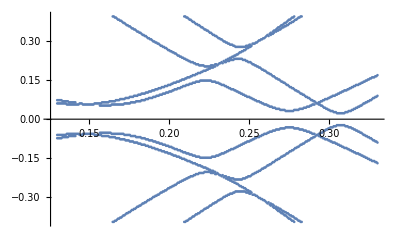

```mathematica
"-----Superconducting state------with Spin-orbit coupling-----";
Super=Flatten[Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\4-Superconducting phase\\4.mat"],1];
Show[ListPlot[Super](*,AL2,Au111*)]
```

```mathematica
"---------------Supercondcuting pairing------------------";
Manipulate[plt=ListLinePlot[

Transpose[(*Table[*)Table[Flatten[{Join[({{kx}, {kx}, {kx}, {kx}, {kx}, {kx}, {kx}, {kx}})],
Sort[Eigenvalues[
({{(kx^2+ky^2) Α-ΔE, 0, f0+fz, fx-ⅈ fy, 0, Δ1, 0, 0}, {0, (kx^2+ky^2) Α-ΔE, fx+ⅈ fy, f0-fz, -Δ1, 0, 0, 0}, {f0+fz, fx-ⅈ fy, G (kx^2+ky^2)-μ, (ⅈ kx+ky) λ, 0, 0, 0, 0}, {fx+ⅈ fy, f0-fz, (-ⅈ kx+ky) λ, G (kx^2+ky^2)-μ, 0, 0, 0, 0}, {0, -Δ1, 0, 0, -((kx^2+ky^2) Α)+ΔE, 0, -f0-fz, -fx-ⅈ fy}, {Δ1, 0, 0, 0, 0, -((kx^2+ky^2) Α)+ΔE, -fx+ⅈ fy, -f0+fz}, {0, 0, 0, 0, -f0-fz, -fx-ⅈ fy, -G (kx^2+ky^2)+μ, (-ⅈ kx+ky) λ}, {0, 0, 0, 0, -fx+ⅈ fy, -f0+fz, (ⅈ kx+ky) λ, -G (kx^2+ky^2)+μ}})],Greater]
}
,{{2},{1}}],{kx,-0.35,0.35,1/1200}](*,{Δ,0,3}]*)]

,Joined->True,PlotRange->{-1.8,1.8},PlotStyle->{Black,Black,Black,Black,Black,Black,Black,Black,Black}];

Show[(*ListPlot[Super],*)plt,PlotRange->{{-0.35,0.35},{-2,2}},AxesOrigin->{0,0}]

,{Α,4.25,100},{ΔE,0.0,4},{G,10,200},{μ,0,6},{ky,0,2},{ λ,0.0,2},{ f0,0,2},{ fx,0,10},{ fy,0,10},{ fz,0,10},{Δ1,0,2}]
```

{μ→0.779376,b→0,c→15.7006,d→0,e→-97.3156,f→0,g→292.485}

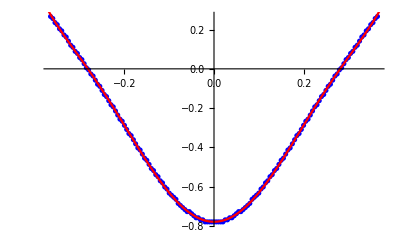

-0.779376+15.7006 k^2-97.3156 k^4+292.485 k^6

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

{μ→0.090666,b→0,c→5.41504,d→0,e→28.1541,f→0,g→-100.518}

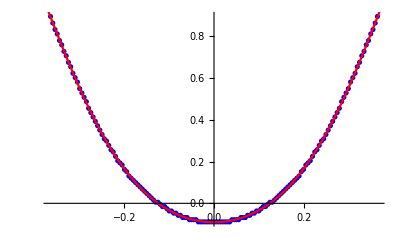

-0.090666+5.41504 k^2+28.1541 k^4-100.518 k^6

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

```mathematica
data2=Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\0-Manipulated data by me\\(Lower band)SOC=0.00.mat"];

data22=Flatten[data2,1];
P1=ListPlot[data22,PlotStyle->{Blue}];
model2=g *k^6+f *k^5+e *k^4+d *k^3+c *k^2+b*k-μ;
fit2=Chop[FindFit[data22,model2,{μ,b,c,d,e,f,g},k]]
(*model=d *k^2+e*k+f;*)
(*fit=FindFit[data3,model,{d,e,f},k]*)
modelf2=Function[{t},Evaluate[model2/.fit2]];
P2=Plot[modelf2[k],{k,-0.37,0.37},PlotStyle->{Red}];
Show[P1,P2]
FindFormula[data22,k]
"%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%"
data3=Import["J:\\2-Updated PhD investigations\\1-PHD\\1-Programing code\\3-Project with Philipp\\3-Fitting infor for band structure\\0-Manipulated data by me\\(Upper band)SOC=0.00.mat"];
data33=Flatten[data3,1];
G1=ListPlot[data33,PlotStyle->{Blue}];
model3=g *k^6+f *k^5+e *k^4+d *k^3+c *k^2+b*k-μ;
fit3=Chop[FindFit[data33,model3,{μ,b,c,d,e,f,g},k]]
(*model=d *k^2+e*k+f;*)
(*fit=FindFit[data3,model,{d,e,f},k]*)
modelf3=Function[{t},Evaluate[model3/.fit3]];
G2=Plot[modelf3[k],{k,-0.37,0.37},PlotStyle->{Red}];
Show[G1,G2]
FindFormula[data33,k]
"%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%"
```

```mathematica
FF[O_]:=FullSimplify[O,{Element[{kx,ky,kz,Δ,ΔE,Α,G,β,γ,λ,f0,k,μ,α,ϵ,Mx,My,Mz,μ1,μ2,α1,α2},Reals]}];


(*λ=0;*)ky=0;(*kx=0;*)
(*mx=0;
my=0;
mz=0;
Zeeman=mx*PauliMatrix[1]+my*PauliMatrix[2]+mz*PauliMatrix[3];*)
fz=0;fy=0;fx=0;
Coup=f0*IdentityMatrix[2]+fx*PauliMatrix[1]+fy*PauliMatrix[2]+fz*PauliMatrix[3];
(*Coup=f0*IdentityMatrix[2]+fx*kx*PauliMatrix[1]+fy*ky*PauliMatrix[2]+fz*kz*PauliMatrix[3];*)

Al=(α1*(kx^2+ky^2)-μ1)*IdentityMatrix[2];
Au=(*(-0.69+16.89 k^2-59.43 k^4+165.60 k^6)IdentityMatrix[2]+*)(α2*(kx^2+ky^2)-μ2)*IdentityMatrix[2]+λ*(ky*PauliMatrix[1]-kx*PauliMatrix[2]);


NS=FF[Join[    Join[Al,Coup ,2]    ,   Join[ConjugateTranspose[Coup],Au,2]      ]    ];


MatrixForm[FullSimplify[NS]]
MatrixForm[FullSimplify[Eigenvalues[NS]]]

MatrixForm[FullSimplify[Eigenvalues[Au]]]
```

(kx^2 α1-μ1 | 0 | f0 | 0
0 | kx^2 α1-μ1 | 0 | f0
f0 | 0 | kx^2 α2-μ2 | ⅈ kx λ
0 | f0 | -ⅈ kx λ | kx^2 α2-μ2)

(1/2 (kx^2 (α1+α2)-kx λ-μ1-μ2-√(4 f0^2+(kx (kx α1-kx α2+λ)-μ1+μ2)^2))
1/2 (kx^2 (α1+α2)-kx λ-μ1-μ2+√(4 f0^2+(kx (kx α1-kx α2+λ)-μ1+μ2)^2))
1/2 (kx (kx (α1+α2)+λ)-μ1-μ2-√(4 f0^2+(kx^2 (α1-α2)-kx λ-μ1+μ2)^2))
1/2 (kx (kx (α1+α2)+λ)-μ1-μ2+√(4 f0^2+(kx^2 (α1-α2)-kx λ-μ1+μ2)^2)))

(kx^2 α2-kx λ-μ2
kx (kx α2+λ)-μ2)

```mathematica
"------Relations between the fitting data and analytical formulas-------";

FullSimplify[Solve[1/2 (-μ1+√(4 f0^2+(μ1-μ2)^2)-μ2)==EAu&&1/2 (-μ1-√(4 f0^2+(μ1-μ2)^2)-μ2)==EAl,{μ1,μ2}]]//MatrixForm
```

(μ1→1/2 (-EAl-EAu+√((EAl-EAu)^2-4 f0^2)) | μ2→1/2 (-EAl-EAu-√((EAl-EAu)^2-4 f0^2))
μ1→1/2 (-EAl-EAu-√((EAl-EAu)^2-4 f0^2)) | μ2→1/2 (-EAl-EAu+√((EAl-EAu)^2-4 f0^2)))

```mathematica
Module[{f0=0.22,EAl=-0.19,EAu=-0.83},MatrixForm[({{Subscript[μ, Au]->1/2 (-EAl-EAu-√((EAl-EAu)^2-4 f0^2))}, {Subscript[μ, Al]->1/2 (-EAl-EAu+√((EAl-EAu)^2-4 f0^2))}})]]
```

(μ_Au→0.277621
μ_Al→0.742379)

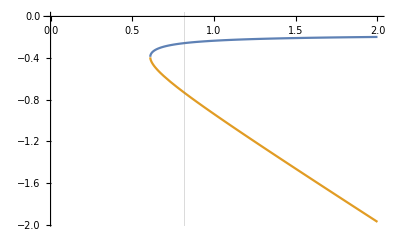

```mathematica
Plot[{1/2 (-0.17+√(-0.1936+(0.17-mu2)^2)-mu2),1/2 (-0.17-√(-0.1936+(0.17-mu2)^2)-mu2)},{mu2,0,2},GridLines->{{0.82}, {}}]
```

```mathematica
FullSimplify[Module[{(*μ1=0.65,μ2=0.3*)},Series[1/2 (kx^2 (α1+α2)-kx λ-μ1-μ2-√(4 f0^2+(kx (kx α1-kx α2+λ)-μ1+μ2)^2)),{kx,0,1}]]]
```

1/2 (-μ1-√(4 f0^2+(μ1-μ2)^2)-μ2)+1/2 λ (-1+(μ1-μ2)/(√(4 f0^2+(μ1-μ2)^2))) kx+O[kx]^2

```mathematica
"-----Relations for the crossing points-------no spin-orbital coupling, no band hybridizations---------";
FullSimplify[[Solve[α1*k^2-μ1==α2*k^2-μ2,k]]]


kx=(√(μ1-μ2))/(√(α1-α2));
FullSimplify[√(4 f0^2+(kx^2 (α1-α2)-μ1+μ2)^2)]
```

FullSimplify⟦{{k→-(√(μ1-μ2))/(√(α1-α2))},{k→(√(μ1-μ2))/(√(α1-α2))}}⟧

2 √(f0^2)

```mathematica
({{1/2 (kx^2 (α1+α2)-kx λ-μ1-μ2-√(4 f0^2+(kx (kx α1-kx α2+λ)-μ1+μ2)^2))}, {1/2 (kx^2 (α1+α2)-kx λ-μ1-μ2+√(4 f0^2+(kx (kx α1-kx α2+λ)-μ1+μ2)^2))}, {1/2 (kx (kx (α1+α2)+λ)-μ1-μ2-√(4 f0^2+(kx^2 (α1-α2)-kx λ-μ1+μ2)^2))}, {1/2 (kx (kx (α1+α2)+λ)-μ1-μ2+√(4 f0^2+(kx^2 (α1-α2)-kx λ-μ1+μ2)^2))}})
```

```mathematica
MatrixForm[FullSimplify[Series[


{1/2 (kx^2 (α1+α2)-kx λ-μ1-μ2-√(4 f0^2+(kx (kx α1-kx α2+λ)-μ1+μ2)^2)),
1/2 (kx^2 (α1+α2)-kx λ-μ1-μ2+√(4 f0^2+(kx (kx α1-kx α2+λ)-μ1+μ2)^2)),
1/2 (kx (kx (α1+α2)+λ)-μ1-μ2-√(4 f0^2+(kx^2 (α1-α2)-kx λ-μ1+μ2)^2)),
1/2 (kx (kx (α1+α2)+λ)-μ1-μ2+√(4 f0^2+(kx^2 (α1-α2)-kx λ-μ1+μ2)^2))
}


,{kx,0,2}]]]
```

(1/2 (-μ1-√(4 f0^2+(μ1-μ2)^2)-μ2)+1/2 λ (-1+(μ1-μ2)/(√(4 f0^2+(μ1-μ2)^2))) kx+1/2 (α1+α2+(-2 f0^2 (λ^2-2 (α1-α2) (μ1-μ2))+(α1-α2) (μ1-μ2)^3)/((4 f0^2+(μ1-μ2)^2)^(3/2))) kx^2+O[kx]^3
1/2 (-μ1+√(4 f0^2+(μ1-μ2)^2)-μ2)+1/2 λ (-1+(-μ1+μ2)/(√(4 f0^2+(μ1-μ2)^2))) kx+1/2 (α1+α2+(2 f0^2 (λ^2-2 (α1-α2) (μ1-μ2))-(α1-α2) (μ1-μ2)^3)/((4 f0^2+(μ1-μ2)^2)^(3/2))) kx^2+O[kx]^3
1/2 (-μ1-√(4 f0^2+(μ1-μ2)^2)-μ2)+1/2 (λ+(λ (-μ1+μ2))/(√(4 f0^2+(μ1-μ2)^2))) kx+1/2 (α1+α2+(-2 f0^2 (λ^2-2 (α1-α2) (μ1-μ2))+(α1-α2) (μ1-μ2)^3)/((4 f0^2+(μ1-μ2)^2)^(3/2))) kx^2+O[kx]^3
1/2 (-μ1+√(4 f0^2+(μ1-μ2)^2)-μ2)+1/2 (λ+(λ (μ1-μ2))/(√(4 f0^2+(μ1-μ2)^2))) kx+1/2 (α1+α2+(2 f0^2 (λ^2-2 (α1-α2) (μ1-μ2))-(α1-α2) (μ1-μ2)^3)/((4 f0^2+(μ1-μ2)^2)^(3/2))) kx^2+O[kx]^3)

```mathematica
Module[{(*This is the data derived for analytical model by mathcing the model and DFT spectrum, See above*) f0=0.22,μ1=0.188,μ2=0.745,λ =0.94,α1=4.25,α2=22},
MatrixForm[{{1/2 (-μ1-√(4 f0^2+(μ1-μ2)^2)-μ2)}, {1/2 (-μ1+√(4 f0^2+(μ1-μ2)^2)-μ2)}, {1/2 (-μ1-√(4 f0^2+(μ1-μ2)^2)-μ2)}, {1/2 (-μ1+√(4 f0^2+(μ1-μ2)^2)-μ2)}}]&&MatrixForm[{{1/2 λ (-1+(μ1-μ2)/(√(4 f0^2+(μ1-μ2)^2)))}, {1/2 λ (-1+(-μ1+μ2)/(√(4 f0^2+(μ1-μ2)^2)))}, {+1/2 (λ+(λ (-μ1+μ2))/(√(4 f0^2+(μ1-μ2)^2)))}, {1/2 (λ+(λ (μ1-μ2))/(√(4 f0^2+(μ1-μ2)^2)))}}]&&MatrixForm[{{1/2 (α1+α2+(-2 f0^2 (λ^2-2 (α1-α2) (μ1-μ2))+(α1-α2) (μ1-μ2)^3)/((4 f0^2+(μ1-μ2)^2)^(3/2)))}, {1/2 (α1+α2+(2 f0^2 (λ^2-2 (α1-α2) (μ1-μ2))-(α1-α2) (μ1-μ2)^3)/((4 f0^2+(μ1-μ2)^2)^(3/2)))}, {1/2 (α1+α2+(-2 f0^2 (λ^2-2 (α1-α2) (μ1-μ2))+(α1-α2) (μ1-μ2)^3)/((4 f0^2+(μ1-μ2)^2)^(3/2)))}, {1/2 (α1+α2+(2 f0^2 (λ^2-2 (α1-α2) (μ1-μ2))-(α1-α2) (μ1-μ2)^3)/((4 f0^2+(μ1-μ2)^2)^(3/2)))}}]
]
Module[{f0=0.22,μ1=0.19,μ2=0.73,λ =0.927,α1=4.1,α2=20.2},


]
```

(-0.821412
-0.111588
-0.821412
-0.111588)&&(-0.83881
-0.10119
0.83881
0.10119)&&(19.9697
6.28034
19.9697
6.28034)